```mathematica
SetDirectory[NotebookDirectory[]];
datav=Import["data_for_voltage.csv"];
datac=Import["data_for_columns.csv"];
datar=Import["data_for_rows.csv"];
dataRC=Import["data_for_columns_and_rows.csv"];
dataVC=Import["data_for_voltage_and_columns.csv"];
dataRV=Import["data_for_rows_and_voltages.csv"];
datamore=Import["data_for_more.csv"];
datamore3=Import["data_for_more3.csv"];
data4=Import["data_for_more4.csv"];
datagears=Import["data_for_gears.csv"];
dataRV2=Import["data_for_v2.csv"];
pillarstandardDeviationistribution=Import["fail_timep.csv"];
gearstandardDeviationistribution=Import["fail_timeg.csv"];
```

Distribution for pillars

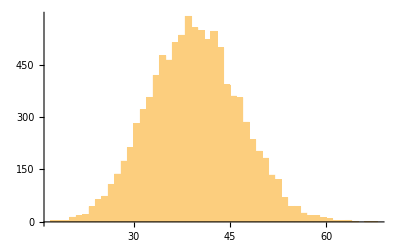

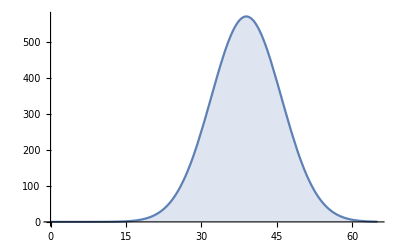

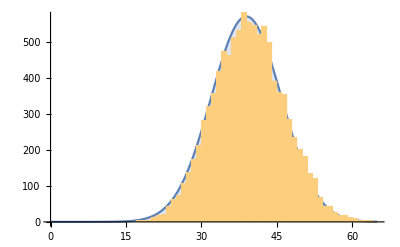

```mathematica
failTimeP=Flatten[pillarstandardDeviationistribution];
HP=Histogram[failTimeP,100]
averagep=0;
averagepsquare=0;
Do[averagep=averagep+failTimeP[[i]];
averagepsquare=averagepsquare+failTimeP[[i]]^2,{i,1,10000}]
averagep=N[averagep/10000];
averagepsquare=averagepsquare/10000;
standardDeviationp=N[averagepsquare-averagep^2]^0.5;
disp=Plot[10000*PDF[NormalDistribution[averagep,standardDeviationp],x],{x,0,65},Filling->Axis]
Show[disp,HP]
```

Distribution for gears

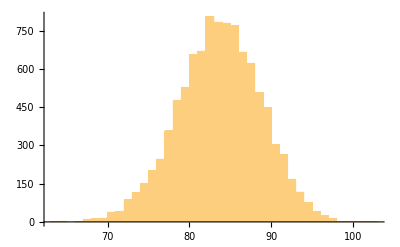

83.1678

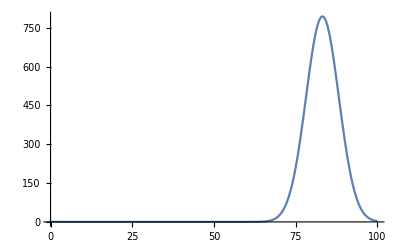

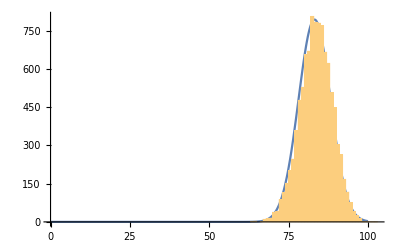

```mathematica
failTimeG=Flatten[gearstandardDeviationistribution];
HG=Histogram[failTimeG,100]

averageG=0;
averageGsquare=0;
Do[averageG=averageG+failTimeG[[i]];
averageGsquare=averageGsquare+failTimeG[[i]]^2,{i,1,10000}]
averageG=N[averageG/10000]
averageGsquare=averageGsquare/10000;
standardDeviationG=N[averageGsquare-averageG^2]^0.5;
disG=Plot[10000*PDF[NormalDistribution[averageG,standardDeviationG],x],{x,0,100},PlotRange->All]
Show[disG,HG]
```

They are both normal distribution, try to see their dependence on the parameters

```mathematica
(*for pillars*)
```

```mathematica
(*plot for v and c*)
```

```mathematica
Do[average={};standardDeviation={};
Do[average=Append[average,{dataVC[[2+i*25+j,1]],dataVC[[2+i*25+j,3]],dataVC[[2+i*25+j,4]]}];standardDeviation=Append[standardDeviation,{dataVC[[2+i*25+j,1]],dataVC[[2+i*25+j,3]],dataVC[[2+i*25+j,5]]^0.5}];
,{j,0,24}];
name=Switch[i,0,"20 rows ",1,"100 rows ",2,
"180 rows "];
pa=ListPlot3D[average,PlotStyle->Gray,PlotLegends->{"average steps of failure"},PlotRange->All,AxesLabel->{"columns","voltage","steps"},PlotLabel->name];
pv=ListPlot3D[standardDeviation,PlotStyle->Red,PlotLegends->{"standardDeviation of failure time"},PlotRange->All,AxesLabel->{"columns","voltage","standardDeviation"},PlotLabel->name];
Print[pa];
Print[pv];
,{i,0,2}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

```mathematica
(*r and v*)
```

```mathematica
Do[average={};standardDeviation={};Do[average=Append[average,{dataRV[[2+i*25+j,2]],dataRV[[2+i*25+j,3]],dataRV[[2+i*25+j,4]]}];
standardDeviation=Append[standardDeviation,{dataRV[[2+i*25+j,2]],dataRV[[2+i*25+j,3]],dataRV[[2+i*25+j,5]]^0.5}];
,{j,0,24}];
name=Switch[i,0,"100 columns ",1,"550 columns ",2,
"1000 columns "];
pa=ListPlot3D[average,PlotStyle->Gray,PlotLegends->{"average steps of failure"},PlotRange->All,AxesLabel->{"rows","voltage","steps"},PlotLabel->name];
pv=ListPlot3D[standardDeviation,PlotStyle->Red,PlotLegends->{"standardDeviation of failure time"},PlotRange->All,AxesLabel->{"rows","voltage","standardDeviation"},PlotLabel->name];
Print[pa];
Print[pv];
,{i,0,2}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

```mathematica
average={};
standardDeviation={};
Do[average=Append[average,{dataRV2[[2+j,2]],dataRV2[[2+j,3]],dataRV2[[2+j,4]]}];
standardDeviation=Append[standardDeviation,{dataRV2[[2+j,2]],dataRV2[[2+j,3]],dataRV2[[2+j,5]]^0.5}];
,{j,0,41}];
name="200 columns ";
pa=ListPlot3D[average,PlotStyle->Gray,PlotLegends->{"average steps of failure"},PlotRange->All,AxesLabel->{"rows","voltage","steps"},PlotLabel->name]
pv=ListPlot3D[standardDeviation,PlotStyle->Red,PlotLegends->{"standardDeviation of failure time"},PlotRange->All,AxesLabel->{"rows","voltage","standardDeviation"},PlotLabel->name]
average={};
standardDeviation={};
Do[average=Append[average,{dataRV2[[2+j,2]],dataRV2[[2+j,3]],dataRV2[[2+j,4]]}];
standardDeviation=Append[standardDeviation,{dataRV2[[2+j,2]],dataRV2[[2+j,3]],dataRV2[[2+j,5]]^0.5}];
,{j,0,11}];
pa=ListPlot3D[average,PlotStyle->Gray,PlotLegends->{"average steps of failure"},PlotRange->All,AxesLabel->{"rows","voltage","steps"},PlotLabel->name]
pv=ListPlot3D[standardDeviation,PlotStyle->Red,PlotLegends->{"standardDeviation of failure time"},PlotRange->All,AxesLabel->{"rows","voltage","standardDeviation"},PlotLabel->name]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
(*c and r*)
```

```mathematica
Do[average={};standardDeviation={};Do[average=Append[average,{datamore[[2+i*64+j,1]],datamore[[2+i*64+j,2]],datamore[[2+i*64+j,4]]}];
standardDeviation=Append[standardDeviation,{datamore[[2+i*64+j,1]],datamore[[2+i*64+j,2]],datamore[[2+i*64+j,5]]^0.5}];
,{j,0,63}];
name=Switch[i,0,"voltage=50 ",1,"voltage=150 ",2,
"voltage=250 ",3,"voltage=20"];
pa=ListPlot3D[average,PlotStyle->Gray,PlotLegends->{"average steps of failure"},PlotRange->All,AxesLabel->{"columns","rows","steps"},PlotLabel->name];
pv=ListPlot3D[standardDeviation,PlotStyle->Red,PlotLegends->{"standardDeviation of failure time"},PlotRange->All,AxesLabel->{"columns","rows","standardDeviation"},PlotLabel->name];
Print[pa];
Print[pv];
,{i,0,3}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«5 more identical outputs»

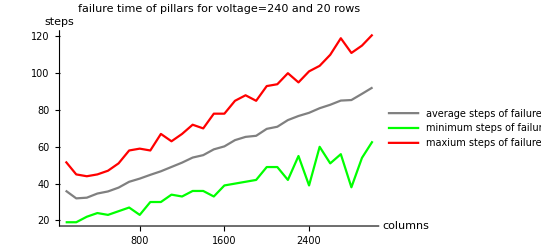

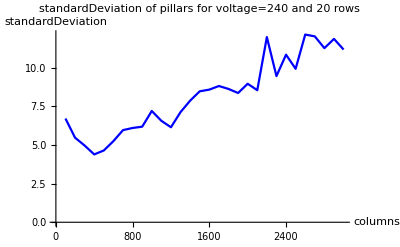

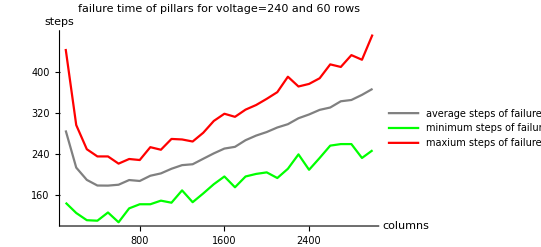

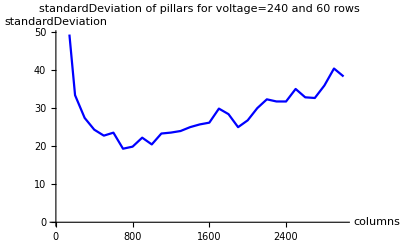

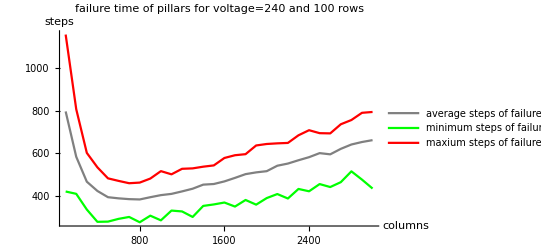

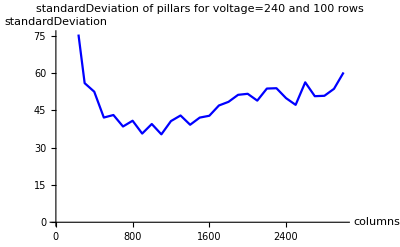

```mathematica
Do[average={};standardDeviation={};mintime={};maxtime={};Do[average=Append[average,{(j+1)*100,data4[[2+30*i+j,4]]}];standardDeviation=Append[standardDeviation,{(j+1)*100,data4[[2+30*i+j,5]]^0.5}];mintime=Append[mintime,{(j+1)*100,data4[[2+30*i+j,6]]}];maxtime=Append[maxtime,{(j+1)*100,data4[[2+30*i+j,7]]}];
,{j,0,29}];
name=Switch[i,0,"failure time of pillars for voltage=240 and 20 rows ",1,"failure time of pillars for voltage=240 and 60 rows ",2,
"failure time of pillars for voltage=240 and 100 rows "];
name2=Switch[i,0,"standardDeviation of pillars for voltage=240 and 20 rows ",1,"standardDeviation of pillars for voltage=240 and 60 rows ",2,
"standardDeviation of pillars for voltage=240 and 100 rows "];
pa=ListLinePlot[average,PlotStyle->Gray,PlotLegends->{"average steps of failure"}];
pvc=ListLinePlot[standardDeviation,PlotStyle->Blue,AxesOrigin->{0.0},AxesLabel->{"columns","standardDeviation"},PlotLabel->name2];
pmin=ListLinePlot[mintime,PlotStyle->Green,PlotLegends->{"minimum steps of failure"}];
pmax=ListLinePlot[maxtime,PlotStyle->Red,PlotLegends->{"maxium steps of failure"}];

Print[Show[pa,pmin,pmax,AxesOrigin->{0,0},PlotRange->Automatic,AxesLabel->{"columns","steps"},PlotLabel->name]];
Print[pvc];
,{i,0,2}]
```

```mathematica
Do[average={};standardDeviation={};Do[average=Append[average,{dataVC[[2+i*25+j,1]],dataVC[[2+i*25+j,3]],dataVC[[2+i*25+j,4]]}];
standardDeviation=Append[standardDeviation,{dataVC[[2+i*25+j,1]],dataVC[[2+i*25+j,3]],dataVC[[2+i*25+j,5]]^0.5}];
,{j,0,24}];
name=Switch[i,0,"20 rows ",1,"100 rows ",2,
"180 rows "];
pa=ListPlot3D[average,PlotStyle->Gray,PlotLegends->{"average steps of failure"},PlotRange->All,AxesLabel->{"columns","voltage","steps"},PlotLabel->name];
pv=ListPlot3D[standardDeviation,PlotStyle->Red,PlotLegends->{"standardDeviation of failure time"},PlotRange->All,AxesLabel->{"columns","voltage","standardDeviation"},PlotLabel->name];
Print[pa];
Print[pv];
,{i,0,2}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

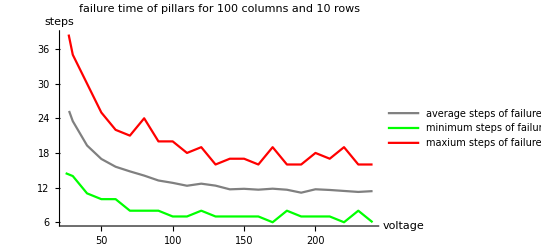

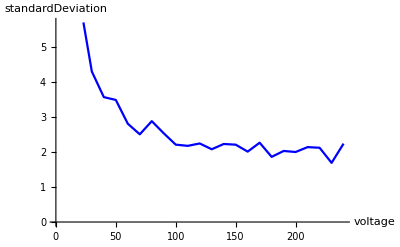

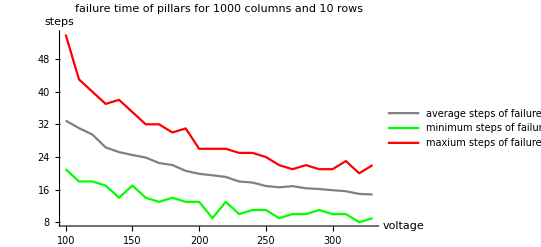

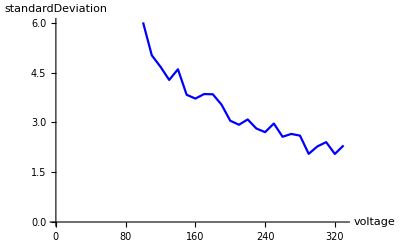

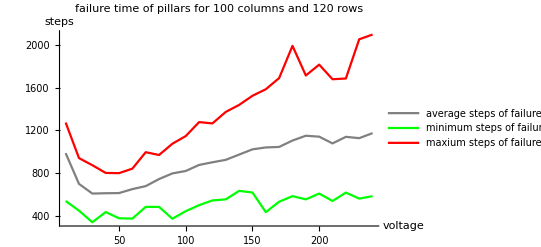

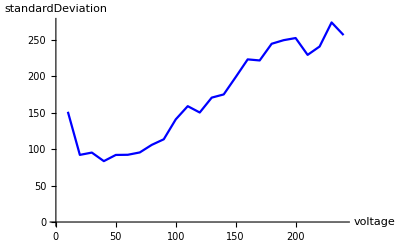

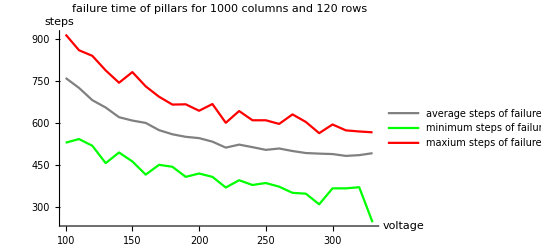

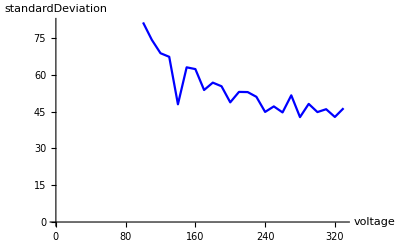

```mathematica
Do[average={};standardDeviation={};mintime={};maxtime={};Do[average=Append[average,{(j+1)*10+Switch[i,0,0,1,90,2,0,3,90],datav[[2+24*i+j,4]]}];standardDeviation=Append[standardDeviation,{(j+1)*10+Switch[i,0,0,1,90,2,0,3,90],datav[[2+24*i+j,5]]^0.5}];mintime=Append[mintime,{(j+1)*10+Switch[i,0,0,1,90,2,0,3,90],datav[[2+24*i+j,6]]}];maxtime=Append[maxtime,{(j+1)*10+Switch[i,0,0,1,90,2,0,3,90],datav[[2+24*i+j,7]]}];
,{j,0,23}];
pa=ListLinePlot[average,PlotStyle->Gray,PlotLegends->{"average steps of failure"}];
pvv=ListLinePlot[standardDeviation,PlotStyle->Blue,AxesOrigin->{0,0},AxesLabel->{"voltage","standardDeviation"}];
pmin=ListLinePlot[mintime,PlotStyle->Green,PlotLegends->{"minimum steps of failure"}];
pmax=ListLinePlot[maxtime,PlotStyle->Red,PlotLegends->{"maxium steps of failure"}];
name=Switch[i,0,"failure time of pillars for 100 columns and 10 rows ",1,"failure time of pillars for 1000 columns and 10 rows ",2,
"failure time of pillars for 100 columns and 120 rows ",3,"failure time of pillars for 1000 columns and 120 rows "];
Print[Show[pa,pmin,pmax,AxesOrigin->{0,0},PlotRange->All,AxesLabel->{"voltage","steps"},PlotLabel->name]];
Print[pvv];
,{i,0,3}]
```

The average:
1. when number of rows increases, need more steps to make the overlap between two columns become zero but resistance decrease, can be seen from the plots, failure time always increases, so the former factor always dominate,
2.when number of columns increases, the resistance increases, but there are more columns likely to fail, the plot shows at first the later dominates, then when the resistance becomes so big, the former dominates, the voltage is higher, the turning point is righter,the number of rows is greater, the turning point is lefter.
3. when voltage increases, the possibility to evaporate and condense increase, so at first I guess when increase voltage, the pillar will always fail faster, but the plot shows if the number of columns is not far greater then number of rows, the pillar will fail slower when voltage increase.
ThInk about in the pillar there are n columns have resistance R and one column has resistance r, r>>R, for example, r=20 R,

```mathematica
P1[R_]=1-1/Exp[U*(20*R)^0.5/(N*R+20*R)];
P2[R_]=1-1/Exp[U*(R)^0.5/(N*R+20*R)];
A=Plot3D[P1[1],{U,1,150},{N,1,100},PlotStyle->Red,PlotLegends->"the shortest column"];
B=Plot3D[P2[1],{U,1,150},{N,1,100},PlotStyle->Green,PlotLegends->"the other columns"];
Print[Show[A,B]]
```

TimeConstrained::timc: Number of seconds 1. is not a positive machine-sized number or Infinity.

Plot3D::invisop: {} must be a valid 2D coordinate.

TimeConstrained::timc: Number of seconds 1. is not a positive machine-sized number or Infinity.

Plot3D::invisop: {} must be a valid 2D coordinate.

-Graphics3D-

we can see when N is small (number of columns is small), the higher the voltage, the closer the two possibility, which ,means the possibility of the shortest column be repaired will be greater, so the pillar will fail slower.

Standard deviation:
The change o standard deviation It is similar to the average.

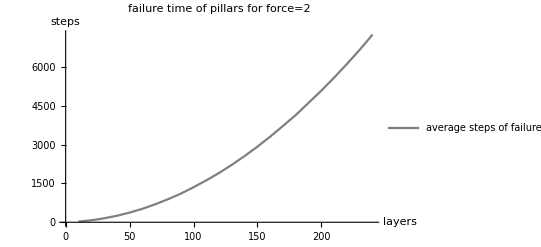

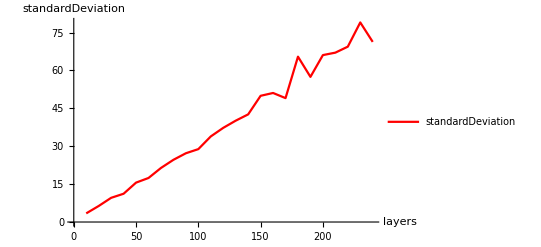

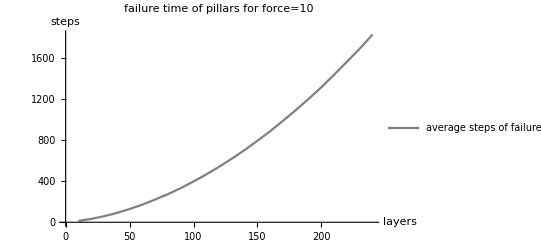

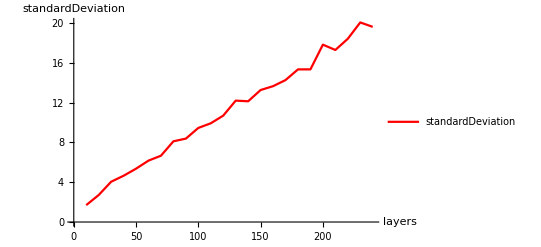

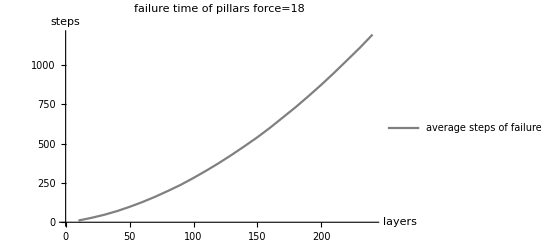

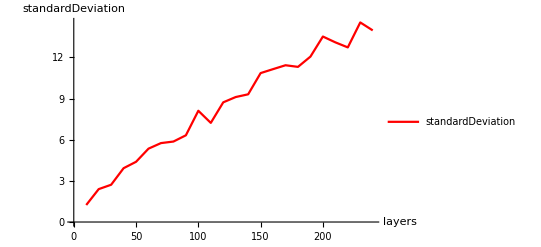

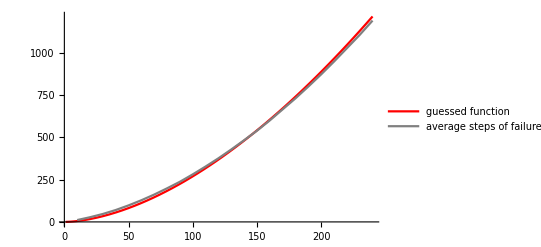

```mathematica
(*like a normaldistribution*)

(*for gears*)
(*number of layers*)
Do[average={};standardDeviation={};
Do[average=Append[average,{datagears[[2+i*24+j,1]],datagears[[2+i*24+j,2]]}];
standardDeviation=Append[standardDeviation,{datagears[[2+i*24+j,1]],datagears[[2+i*24+j,3]]^0.5}];
,{j,0,23}];
name=Switch[i,0,"failure time of pillars for force=2 ",1,"failure time of pillars for force=10 ",2,
"failure time of pillars force=18 "];
pa=ListLinePlot[average,PlotStyle->Gray,AxesOrigin->{0,0},PlotLegends->{"average steps of failure"},PlotRange->All,AxesLabel->{"layers","steps"},PlotLabel->name];
pv=ListLinePlot[standardDeviation,PlotStyle->Red,AxesOrigin->{0,0},PlotLegends->{"standardDeviation"},PlotRange->All,AxesLabel->{"layers","standardDeviation"}];
Print[pa];
Print[pv];
,{i,0,2}]
p=Show[Plot[0.098*  x^1.72,{x,1,240},PlotStyle->Red,AxesOrigin->{0,0},PlotLegends->{"guessed function"}],pa,PlotRange->All]
```

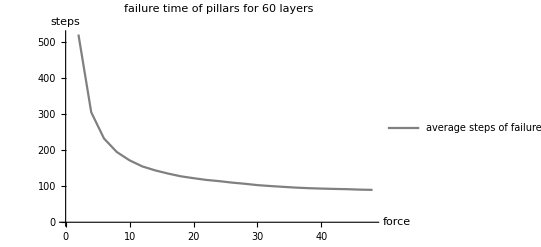

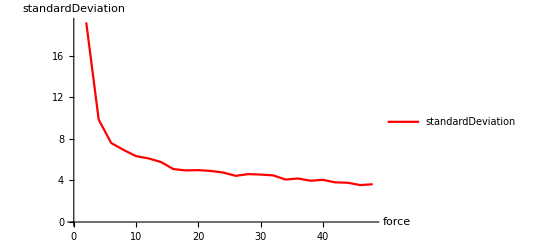

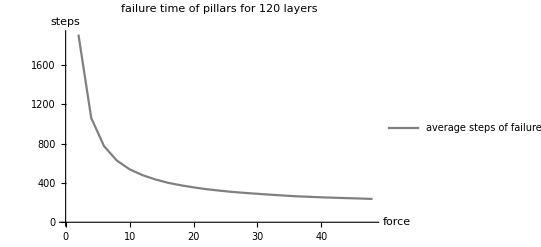

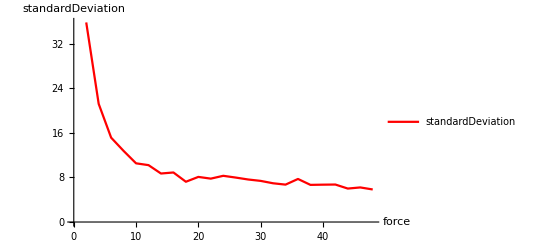

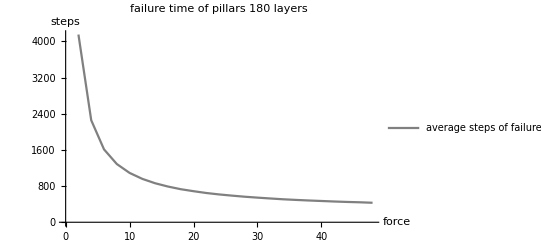

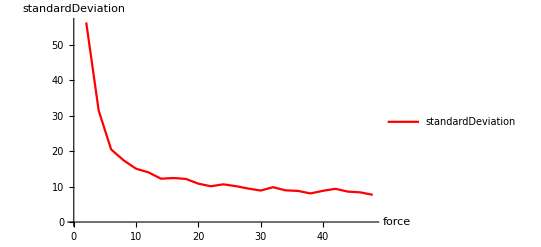

```mathematica
(*force*)
Do[average2={};standardDeviation={};
Do[average2=Append[average2,{2*(j+1),datagears[[74+i*24+j,2]]}];
standardDeviation=Append[standardDeviation,{2*(j+1),datagears[[74+i*24+j,3]]^0.5}];
,{j,0,23}];
name=Switch[i,0,"failure time of pillars for 60 layers ",1,"failure time of pillars for 120 layers ",2,
"failure time of pillars 180 layers "];
pa=ListLinePlot[average2,PlotStyle->Gray,AxesOrigin->{0,0},PlotLegends->{"average steps of failure"},PlotRange->All,AxesLabel->{"force","steps"},PlotLabel->name];
pv=ListLinePlot[standardDeviation,PlotStyle->Red,AxesOrigin->{0,0},PlotLegends->{"standardDeviation"},PlotRange->All,AxesLabel->{"force","standardDeviation"}];
Print[pa];
Print[pv];
,{i,0,2}]
```

```mathematica
As the number of layers increase, the average and standard deviation both increase like a polynomial function.
As the force increase,
both decrease.
```